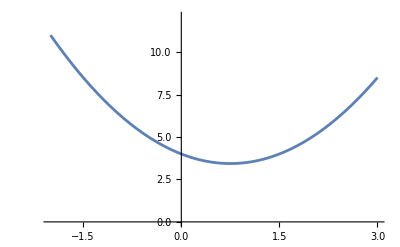

```mathematica
f[x_]:=4-1.5x+x^2;
range={-2,3,0.1};

pRange=AbsoluteOptions[Plot[f[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]]*{{1, 1}, {0, 1.1}};
Plot[f[x],{x, range[[1]], range[[2]]}, PlotRange->pRange]
```

```mathematica
approximatingPoints[xii_,w_,n_:20]:=Join[Transpose[{NestList[f, xii, n], NestList[f, w, n]}],Transpose[{NestList[f, w, n], NestList[f, f[xii], n]}]]

LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]

approxFunc[xii_, w_]:=LinearSpline[approximatingPoints[xii, w]]
errorFunc[xii_, w_]:=Quiet[With[{af=approxFunc[xii,w]},Sum[(af[af[x]]-f[x])^2, {x, range[[1]], range[[2]], range[[3]]}]],General::munfl]
```

```mathematica
xiiRange=range;wRange=range; (*Tweak these for faster initial evaluation times *)

search[]:=(
points=ParallelTable[errorFunc[xii, w],{xii, xiiRange[[1]],  xiiRange[[2]],  xiiRange[[3]]}, {w, wRange[[1]],  wRange[[2]],  wRange[[3]]}];
minI=First[Position[points,Min[points],2]];
minP={xiiRange[[1]]+minI[[1]]xiiRange[[3]], wRange[[1]]+minI[[2]]wRange[[3]]};
minV=errorFunc@@minP;

xiiRange={minP[[1]]-xiiRange[[3]], minP[[1]]+xiiRange[[3]], 0.5xiiRange[[3]]};
wRange={minP[[2]]-wRange[[3]], minP[[2]]+ wRange[[3]], 0.5wRange[[3]]};

minV
);
```

```mathematica
PrintTemporary["The first step takes way longer than future steps"];
progress=PrintTemporary["0% Complete"];
numIterSearch=20;
Table[NotebookDelete[progress]; progress=PrintTemporary[ToString[Round[100*(iter-1)/numIterSearch]]<>"% Complete"]; search[], {iter,numIterSearch}]
```

{251.942,230.212,225.923,223.959,223.291,223.037,222.746,222.603,222.533,222.499,222.481,222.473,222.468,222.466,222.465,222.465,222.464,222.464,222.464,222.464}

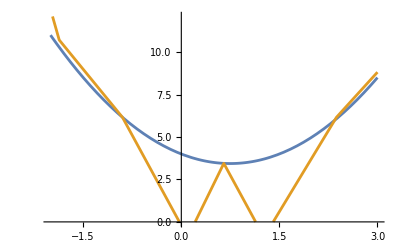

```mathematica
aFunc= approxFunc@@minP;
Plot[{f[x], aFunc[aFunc[x]]}, {x, range[[1]], range[[2]]}, PlotRange->pRange]
```

```mathematica
minP
```

{0.65,-0.9}

## Numerical minimization

```mathematica
range[[3]]=0.01;

aFunc= approxFunc@@minP;
xVals=Range@@range;
fVals=f/@xVals;
aVals=aFunc[aFunc[#]]&/@xVals;

plots={};
funcFromVals[vals_]:=LinearSpline[Transpose[{xVals,  vals}]]
```

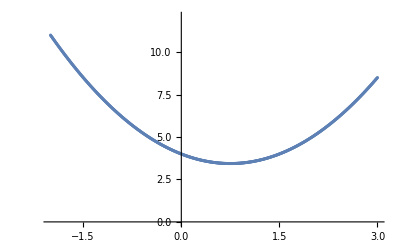

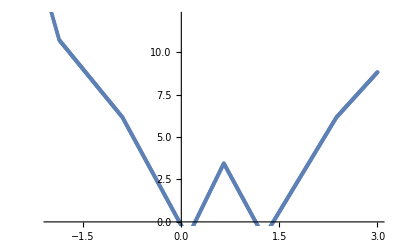

```mathematica
PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}], PlotRange->pRange], Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]}, PlotRange->pRange]}]
PlotVals[fVals]
PlotVals[aVals]
```

```mathematica
imax=10;jmax=2; (* j is how many steps to run in between plots, i is how many plots to generate *)

progress=PrintTemporary["0% Complete"];
Table[Table[
aFunc=funcFromVals[aVals];
nestedApproxVals=aFunc[aFunc[#]]&/@xVals;
deltaVals=fVals-nestedApproxVals;
newApproxVals=aVals+0.1*deltaVals;
aVals=newApproxVals;
NotebookDelete[progress];
progress=PrintTemporary[ToString[Floor[100*(i*jmax+j)/((imax+1)*(jmax))]]<>"% Complete"];,{j, jmax}];
plots=AppendTo[plots,Plot[aFunc[aFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->Small, PlotRange->pRange]];
, {i,imax}];
```

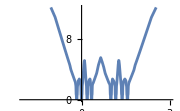
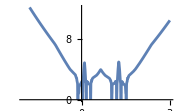
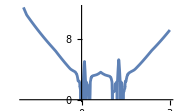
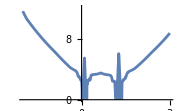
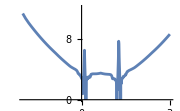
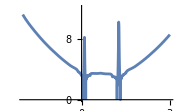
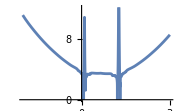
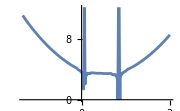

```mathematica
plots
```

-Graphics-

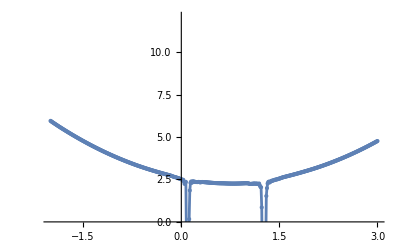

```mathematica
PlotVals[fVals]
PlotVals[aVals]
```

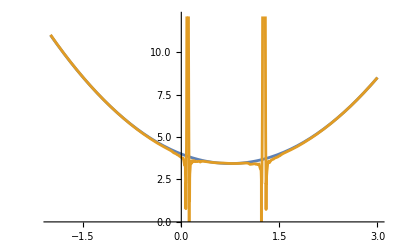

```mathematica
Plot[{f[x], aFunc[aFunc[x]]}, {x, range[[1]], range[[2]]}, PlotRange->pRange]
```